## Harvest model with Type III response - single trajectories - large noise

## Setup and Universal Parameters

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/fold_harvest/figures"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* get package for user-defined functions *)
Get["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/packages/my_functions/spectral_functions.wl"];
```

```mathematica
(* Universal simulation parameters *)
dt=0.1; (* time step for stochastic simulation *)
dt2 = 1; (* time separation for indicator calculation - increase to speed up computation *)
tmax=1000 ; (* max time in simulation *)
numSims=3; (* number of realisations to average over *)

(* options for EWS calculation *)
detrendOp=1; (* 1 for yes, 0 for no *)
bandWidth=0.2; (* for Gaussian filtering (as a percentage) *)
rollWindow=0.25;(* for indicator calculation *)

(* hamming window size and length *)
hamLength=20; 
hamOffset=5; 


(* lag autocorrelation *)
numComps=tmax/dt+1; (* number of components in simulation *)
tauVals={1,2};

psdTime=250;(* time which psd computed *)

(* Figure display parameters *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={60,50,20,20};  (* image padding *)
indexPos=Scaled[{0.065,1.10}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)
```

## Model Analysis

Use bistable harvesting model : dx/dt = rx(1-x) - hx^2/(s^2 +x^2)

```mathematica
(* Clear variable names *)
Clear[f,x,r,h,s]
$Assumptions={x,r,a,s}∈Reals;
```

```mathematica
(* Dynamic equations *)
f[x_]:=r x(1-x) - h x^2/(s^2+x^2);
```

```mathematica
f[x]
```

r (1-x) x-(h x^2)/(s^2+x^2)

```mathematica
(* Parameter values *)
r=1;
s=0.1;
```

```mathematica
(* Find equilibiria *)
equi=Solve[f[x]==0,x]//Quiet;
```

```mathematica
equi/.{h->0.1}
```

{{x→0.},{x→0.0555458+0.0903572 ⅈ},{x→0.888908+0. ⅈ},{x→0.0555458-0.0903572 ⅈ}}

```mathematica
(* Initial stable equilibrium *)
equiInit=Re[x/.equi[[3]]];

(* Bifurcation point *)
{xbif,hbif}=Re[{x,h}/.Solve[f[x]==0&&f'[x]==0][[3]]]//Quiet
```

{0.478128,0.260437}

```mathematica
(* Eigenvalue at equilibrium point *)
Clear[λ]
λ[a_]=D[f[x],x]/.{x->equiInit};
```

```mathematica
(* Phase portrait, hval control parameter *)
Manipulate[
Plot[f[x]/.{r->rval,h->hval,s->sval},{x,0,1},
PlotRange->{-0.2,0.2},
AxesLabel->{"x","f(x)"},
LabelStyle->TMBFS12],
{{rval,1},0.5,1.5},{{hval,0},0,0.4},{{sval,0.1},0.05,0.3}];
```

## Stochastic Simulation

Stochastic model 
dX = rX(1-X) -hX^2/(s^2+X^2)

### Key parameters

```mathematica
a1=0.05;(* noise intensity *)
r=1; (* model parameteres *)
s=0.1;
hl=0.15; (* min value of control parameter *)
hh=0.15; (* max value of control parameter *)
x0=equiInit/.h->hl; (* initial condition *)
seed=10; (* seed number *)

(* lag autocorrelation *)
numComps=tmax/dt+1;
tauVals={1,2};
```

### Model Dynamics

```mathematica
Clear[f]
f[x_,h_]:=r x(1-x)-h x^2/(s^2+x^2);
```

### Stochastic Simulation

```mathematica
(* evolution of control param - harvesting rate *)
Clear[h,t]
h[t_]:=((hh-hl)/tmax) t +hl
```

```mathematica
(* number of components in simulation *)
nComps=Floor[tmax/dt]+1;
```

```mathematica
(* array for output time-series *)
x=ConstantArray[0,{numSims,nComps}];
t=Range[0,tmax,dt];
```

```mathematica
(* intitial condition *)
x[[;;,1]]=x0;
```

```mathematica
(* noise values *)
noiseVals=RandomVariate[NormalDistribution[0,1],{numSims,nComps}];
```

```mathematica
(* set up counter *)
For[j=1,j≤numSims,j++,
For[i=1,i≤nComps-1,i++,
(* update state variable *)
x[[j,i+1]]=x[[j,i]]+f[x[[j,i]],h[t[[i]]]]dt+a1*Sqrt[dt]*noiseVals[[j,i]];
(* make sure state variable stays above x=0 *)
If[x[[j,i+1]]≤0,x[[j,i+1]]=0];
]
]
```

```mathematica
(* dimensions of xVals - (num realisations, tstep)  *)
x//Dimensions
```

{3,10001}

```mathematica
(* assign *)
tValsFull=t;
xValsFull=x;
```

### Filter time-series to improve computation time

```mathematica
(* Filter time-series seperation of dt2 to make analysis computationally feasible *)
tVals=Take[tValsFull,{1,Length[tValsFull],dt2/dt}];
xVals=Take[xValsFull,All,{1,Length[tValsFull],dt2/dt}];
```

### Single realisation plots

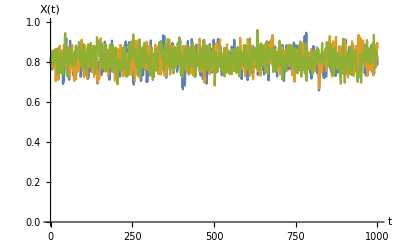

```mathematica
(* make plot of single realisation in x *)
plotX=ListPlot[Table[{tVals,xVals[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","X(t)"},
PlotRange->{0,1}]
```

## Traditional EWS

### Detrend - fit Gaussian

```mathematica
(* work with data only up to bifurcation (tcrit) *)
tcrit=339.805*(10/4) (* same as for transient investigation *)
idxCrit=FirstPosition[tVals,t_/;t≥tcrit][[1]]-1;
tValsShort=tVals[[1;;idxCrit]];
```

849.513

```mathematica
dataFitX=ConstantArray[x0,{numSims,idxCrit}];
```

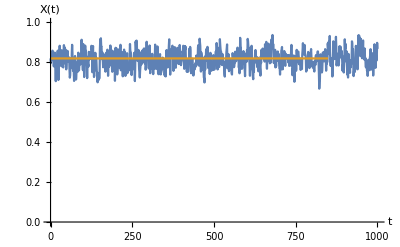

```mathematica
(* plot of a single X realisation fitted *)
fitPlotX=ListPlot[{{tVals,xVals[[2]]}ᵀ,{tValsShort,dataFitX[[2]]}ᵀ},
Joined->True,
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","X(t)"},
PlotRange->{{0,tmax},{0,1}}]
```

### Residuals

```mathematica
residualsX=xVals[[;;,1;;idxCrit]]-dataFitX;
residualsX//Dimensions
```

{3,850}

```mathematica
(* plot of a single realisation *)
residPlotX=ListPlot[{tValsShort,residualsX[[1]]}ᵀ,
Joined->True,
Filling->Axis,
AxesLabel->{"t","Res"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},All}];
```

### Variation of Residuals

```mathematica
(* number of components in rolling window *)
windowComps=Floor[rollWindow*Length[tVals]];
```

```mathematica
(* compute variance of residuals - has form [v1;v2;v3;...;vn] *)
varSeriesX=Table[MovingMap[Variance,residualsX[[i]],windowComps],{i,1,numSims}];
varSeriesX//Dimensions
```

{3,600}

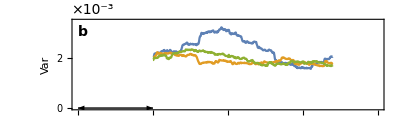

```mathematica
(* plot individual realisations *)
varPlotX=ListPlot[Table[{tValsShort[[windowComps+1;;]],varSeriesX[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},{0,0.0035}},
FrameLabel->{{"Var",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameTicks->{{{{0,0},{0.001,1},{0.002,2},{0.003,3}},Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
Text[Style["×10^-3",14],indexPos],
Text[Style["b",14,Bold],Scaled[labelLetterPos]]}]
```

### Autocorrelation of Residuals at lag 1

```mathematica
(* form [a1;a2;,,,;an] *)
acSeriesX=Table[MovingMap[CorrelationFunction[#,1]&,residualsX[[i]],windowComps],{i,1,numSims}];  
acSeriesX//Dimensions
(* sim number, lag number, time value *)
```

{3,600}

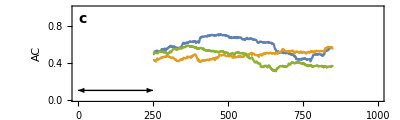

```mathematica
(* ac-1 plot of single realisations *)
acPlotX=ListPlot[Table[{tValsShort[[windowComps+1;;]],acSeriesX[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
LabelStyle->14,
Frame->True,
FrameLabel->{{"AC",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
PlotRange->{{0,tmax},{0,1}},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0.1}],Scaled[{0,arHeight},{windowComps*dt2,0.1}]}],
Text[Style["",14],Scaled[{1.08,-0.05}]],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

## Power Spectrum EWS

### Compute power spectrum over rolling window with same offset has Hamming windows

```mathematica
(* evaluate power spectrum of residuals in rolling window with the offset the same as hamOffset *)
pSpecSeriesX=Table[MovingMap[TBPowerSpecWelch[{#,dt2,hamLength,hamOffset}]&,residualsX[[i]],{windowComps,Left,hamOffset}],{i,1,numSims}];
```

```mathematica
(* frequncy values of power spectra *)
ωVals=pSpecSeriesX[[1,1,1]];
```

### Plot of individual realisations

```mathematica
pSpecSeriesX//Dimensions
```

{3,120,2,21}

```mathematica
tcrit
```

849.513

```mathematica
(* plot times to use *)
plotTimes=Range[dt2*windowComps,tcrit-toffset,hamOffset*2]
```

{250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500,510,520,530,540,550,560,570,580,590,600,610,620,630,640,650,660,670,680,690,700,710,720,730,740,750,760,770,780,790}

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{"TemperatureMap",timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

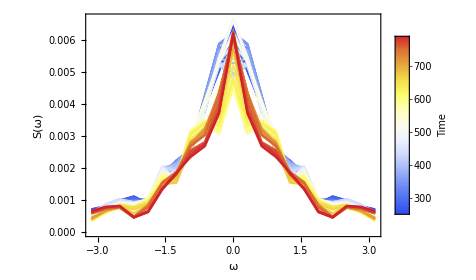

```mathematica
(* normalise to map to a colour *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
psdSinglePlot=ListLinePlot[Table[Transpose[pSpecSeriesX[[2,tindex]]],{tindex,1,Length[plotTimes]}],
PlotRange->All,
PlotStyle->Thread@{ColorData["TemperatureMap"]/@plotTimesUnit},
LabelStyle->13,
Frame->True,
AxesOrigin->{0,0},
ImagePadding->{{70,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.7,
FrameLabel->{{"S(ω)",None},{"ω",None}},
PlotLegends->Placed[colLegend,Scaled[{0.9,0.55}]]]
```

### Max-frequency component

```mathematica
pSpecSeriesX//Dimensions
```

{3,120,2,21}

```mathematica
(* Subscript[S, max] data *)
specMax=Table[Max[pSpecSeriesX[[i,j,2,;;]]],{i,1,numSims},{j,1,Dimensions[pSpecSeriesX][[2]]}];
specMax//Dimensions
```

{3,120}

```mathematica
tValsShort[[windowComps+1;;-1;;hamOffset]]//Dimensions
```

{120}

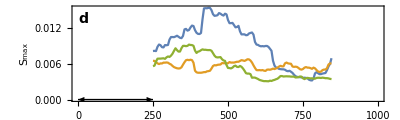

```mathematica
(* plot individual realisations *)
specMaxPlot=ListPlot[Table[{tValsShort[[windowComps+1;;-1;;hamOffset]],specMax[[i]]}ᵀ,{i,1,numSims}],
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},All},
FrameLabel->{{"S_max",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
(*FrameTicks->{{{{0,0},{0.001,1},{0.002,2},{0.003,3},{0.004,4}},Automatic},{Automatic,Automatic}}*)
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
(*Text[Style["×10^-3",14],indexPos],*)
Text[Style["d",14,Bold],Scaled[labelLetterPos]]}]
```

### Hopf-AIC weight

```mathematica
?TBHopfAIC
```

TBHopfAIC[pSpec] fits the analytical forms for the Hopf and Fold bifurcation to the data in pSpec. 
It then outputs the AIC weight that corresponds to the Hopf fit. 
Note the Hopf fit is restricted such that S(ω_0)> 2 S(0). This stops the model being selected for the Fold spectrum.
pSpec = {freqVals,powerVals}
Outputs = hopfAICweight
AIC weights can be interpreted as the probability that the fitted model is the best model (in the AIC sense)

```mathematica
pSpecSeriesX//Dimensions
```

{3,120,2,21}

```mathematica
?TBHopfAIC
```

TBHopfAIC[pSpec] fits the analytical forms for the Hopf and Fold bifurcation to the data in pSpec. 
It then outputs the AIC weight that corresponds to the Hopf fit. 
Note the Hopf fit is restricted such that S(ω_0)> 2 S(0). This stops the model being selected for the Fold spectrum.
pSpec = {freqVals,powerVals}
Outputs = hopfAICweight
AIC weights can be interpreted as the probability that the fitted model is the best model (in the AIC sense)

```mathematica
Timing[TBFitSpec[pSpecSeriesX[[1,10]]]]
```

{0.456487,{1.,2.31796×10^-19,3.43487×10^-17}}

```mathematica
(* compute AIC weights - LONG SIMULATION *)
aicWeightSeriesX=Monitor[
Table[Quiet[TBFitSpec[pSpecSeriesX[[i,j]]]],{i,1,numSims},{j,1,Dimensions[pSpecSeriesX]⟦2⟧}],
{ProgressIndicator[i,{1,numSims}],ProgressIndicator[j,{1,Dimensions[pSpecSeriesX]⟦2⟧}]}];
```

```mathematica
aicWeightSeriesX//Dimensions
```

{3,120,3}

```mathematica
pSpecSeriesX//Dimensions
```

{3,120,2,21}

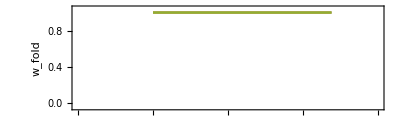

```mathematica
(* plot of individual realisations for wfold *)
aicFoldPlot=ListPlot[Table[
{tValsShort[[windowComps+1;;-1;;hamOffset]],aicWeightSeriesX[[i,;;,1]]}ᵀ,{i,{1,2,3}}],
Joined->True,
LabelStyle->14,
PlotRange->{{0,tmax},{-0.05,1.05}},
Frame->{{True,True},{True,True}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{{"w_fold",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameTicks->{{All,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3]
```

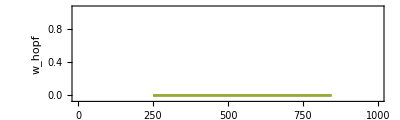

```mathematica
(* plot of individual realisations for whopf *)
aicHopfPlot=ListPlot[Table[
{tValsShort[[windowComps+1;;-1;;hamOffset]],aicWeightSeriesX[[i,;;,2]]}ᵀ,{i,{1,2,3}}],
Joined->True,
LabelStyle->14,
PlotRange->{{0,tmax},{-0.05,1.05}},
Frame->{{True,True},{True,True}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{{"w_hopf",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{All,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3]
```

## Bifurcation diagram

### Specifications

```mathematica
(* Import data *)
rawdata=Import["../bifurcation_data/fold.dat"];

lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{-1,0.5},{-1,1}}; (* plot range *)
(*frLabel={"μ","x"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Output

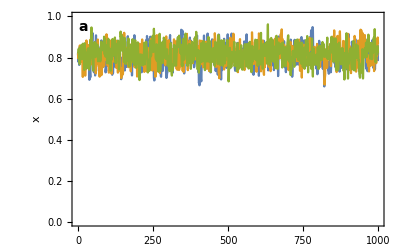

```mathematica
(* Incorporate with simulation and region of psd computation *)
lineStyle={Red,Opacity[0.4]};
sqHeight=0.12;
trajVal=0.7;

bifTrajX=Show[plotX,
PlotRange->{{0,tmax},{0,1}},
LabelStyle->14,
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"x",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["a",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle]}
]
```

## Combined Plot

```mathematica
foldEwsPlot=Grid[{{bifTrajX,psdSinglePlot},{varPlotX,aicFoldPlot},{acPlotX,aicHopfPlot},{specMaxPlot,SpanFromAbove}},Spacings->{0,-0.6}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Export["single_largenoise_stat.png",foldEwsPlot,ImageResolution->200];
```